# Tarea 1, Mat1620L

## Preguntas

### 1) Aproximación local mediante Taylor (terminada)

#### Solución

Texto

x-x^3/3+x^5/5-x^7/7+x^9/9-x^11/11

x-x^3/3+x^5/5-x^7/7+x^9/9-x^11/11+x^13/13-x^15/15+x^17/17-x^19/19+x^21/21

x-x^3/3+x^5/5-x^7/7+x^9/9-x^11/11+x^13/13-x^15/15+x^17/17-x^19/19+x^21/21-x^23/23+x^25/25-x^27/27+x^29/29-x^31/31+x^33/33-x^35/35+x^37/37-x^39/39+x^41/41

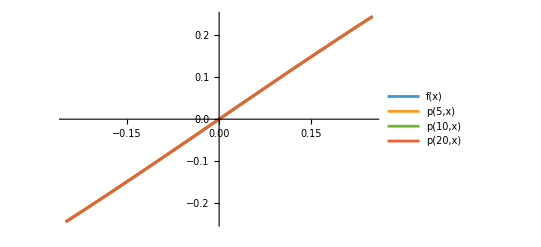

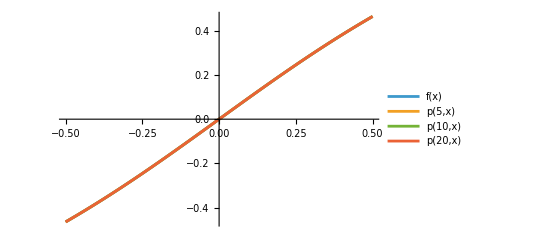

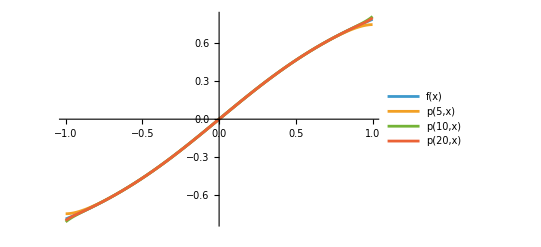

```mathematica
ClearAll["Global`*"]
f[x_]:=ArcTan[x]
p[n_,x_]:=Sum[(-1)^k x^(2 k+1)/(2 k+1),{k,0,n}]
p[5,x]
p[10,x]
p[20,x]

Plot[{f[x],p[5,x],p[10,x],p[20,x]},{x,-0.25,0.25},
PlotLegends->"Expressions"]

Plot[{f[x],p[5,x],p[10,x],p[20,x]},{x,-0.5,0.5},
PlotLegends->"Expressions"]

Plot[{f[x],p[5,x],p[10,x],p[20,x]},{x,-1,1},PlotLegends->"Expressions"]
```

### 2) Primera estrategia: una reducción de rango. (terminada)

#### Solución

Texto

x-x^3/3+x^5/5-x^7/7+x^9/9-x^11/11+x^13/13-x^15/15+x^17/17-x^19/19+x^21/21

(-1+x)/(1+x)

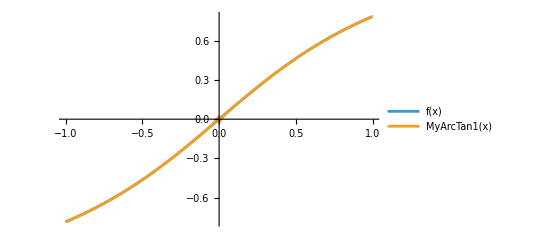

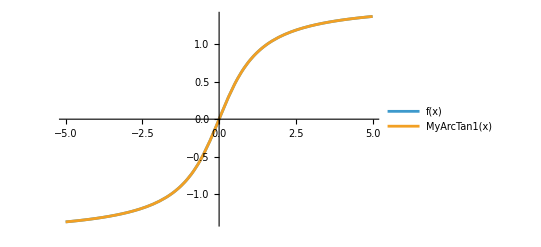

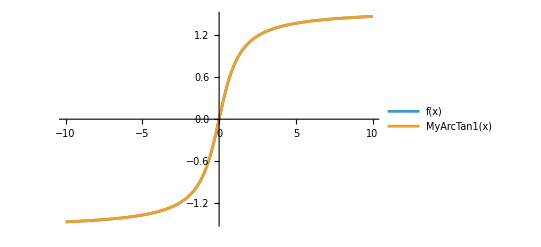

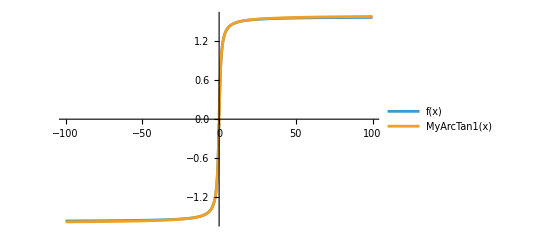

```mathematica
ClearAll["Global`*"]
f[x_]:=ArcTan[x]
p[n_,x_]:=Sum[(-1)^k x^(2 k+1)/(2 k+1),{k,0,n}]
p10[x_] = p[10,x]
T[x_] = (x-1)/(x+1)
MyArcTan1[x_] := Piecewise[{{ (Pi/4) + p10[T[x]],x> 0},{-MyArcTan1[-x],x<0},{0, x==0}}]

Plot[{f[x], MyArcTan1[x]},{x,-1,1},PlotLegends->"Expressions"]
Plot[{f[x], MyArcTan1[x]},{x,-5,5},PlotLegends->"Expressions"]
Plot[{f[x], MyArcTan1[x]},{x,-10,10},PlotLegends->"Expressions"]
Plot[{f[x], MyArcTan1[x]},{x,-100,100},PlotLegends->"Expressions"]
```

Describa el comportamiento observado.
R:  En la gráfica 1, de -1 a 1, la función MyArcTan1(x) presenta un corte al aproximarse a cero, sube un poco antes de cero, y luego reanuda la función un poco más abajo, pero nunca toca el (0,0) a diferencia de 
Arctan(x).

### 3) Segunda estrategia: reducción mediante el recíproco. (terminada)

#### Solución

Texto

x-x^3/3+x^5/5-x^7/7+x^9/9-x^11/11+x^13/13-x^15/15+x^17/17-x^19/19+x^21/21

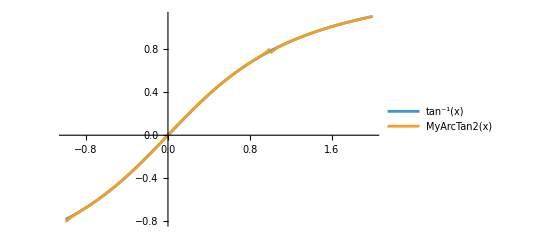

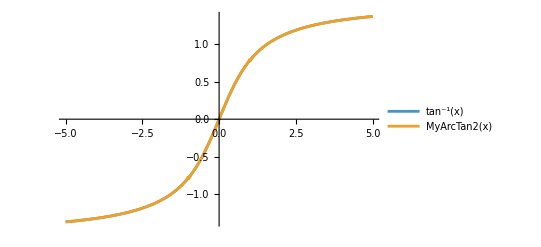

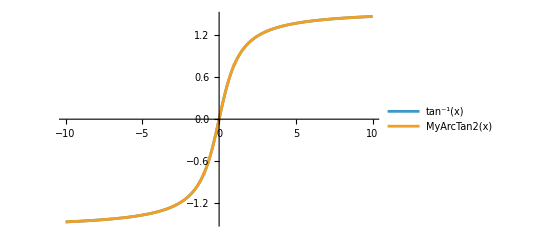

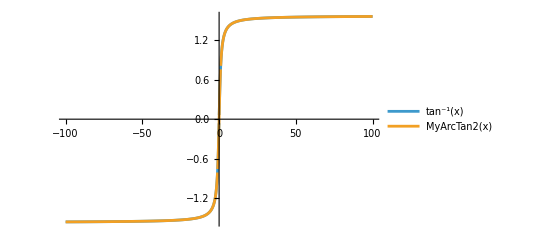

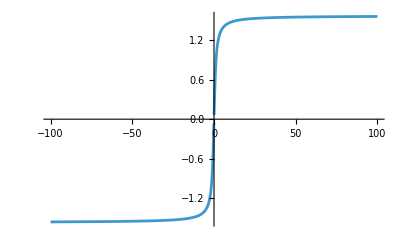

```mathematica
ClearAll["Global`*"]
p[n_,x_]:=Sum[(-1)^k x^(2 k+1)/(2 k+1),{k,0,n}]
p10[x_] = p[10,x]
g[x_] := (Pi/2) -p10[1/x]
h[x_] := -(Pi/2) -p10[1/x]
MyArcTan2[x_] := Piecewise[{{ g[x],x> 1},{h[x],x<-1},{p10[x], -1<=x<=1}}]
Plot[{ArcTan[x],MyArcTan2[x]},{x,-1,2},PlotLegends->"Expressions"]
Plot[{ArcTan[x],MyArcTan2[x]},{x,-5,5},PlotLegends->"Expressions"]
Plot[{ArcTan[x],MyArcTan2[x]},{x,-10,10},PlotLegends->"Expressions"]
Plot[{ArcTan[x],MyArcTan2[x]},{x,-100,100},PlotLegends->"Expressions"]
Plot[{ArcTan[x]},{x,-100,100},PlotLegends->"Expressions"]
```

Podemos observar en la 1ra y 2da gráfica que al llegar a x=1, la función MyArcTan2 se “corta” en dos trazos, o sea, es discontinua, para luego continuar con la aproximación a Arctan(x).

### 4) Tercera estrategia: reducción adaptativa del argumento.

#### Solución

A partir de la desigualdad |(x-1)/(x+1)| <= 0.5, x está en el intervalo [1/3, 3]

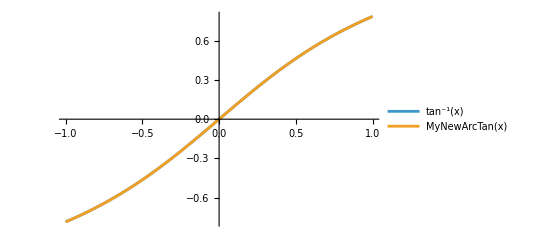

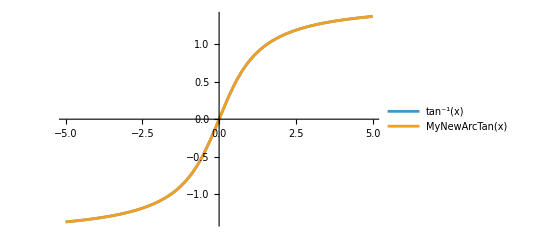

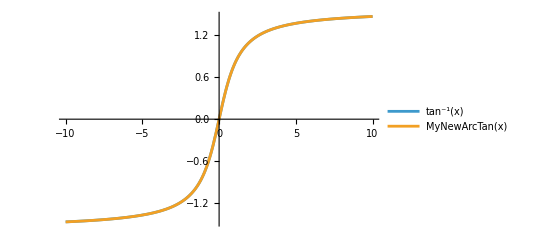

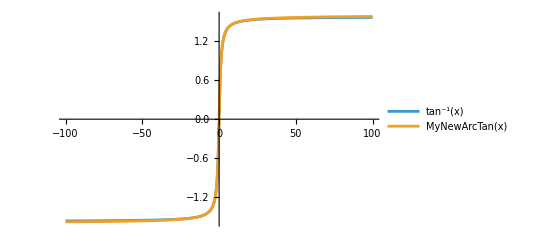

```mathematica
ClearAll["Global`*"]
p[n_,x_]:=Sum[(-1)^k x^(2 k+1)/(2 k+1),{k,0,n}]
p10[x_]:=p[10,x]
T[x_]:=(x-1)/(x+1)
x1[x_]:=T[x]
x2[x_]:=T[x1[x]]

(*A partir de la desigualdad|(x-1)/(x+1)| <=0.5,x está en el intervalo[1/3,3]*)
MyNewArcTan[x_]:=Piecewise[{{p10[x],0<=x<=0.5},{(Pi/4)+p10[x1[x]],x>0.5},{(Pi/4)+p10[x1[x]],Abs[x1[x]]<=0.5},{(Pi/2)+p10[x2[x]],x>0.5&&x1[x]>0.5},{-MyNewArcTan[-x],x<0}}]
Plot[{ArcTan[x],MyNewArcTan[x]},{x,-1,1},PlotLegends->"Expressions"]
Plot[{ArcTan[x],MyNewArcTan[x]},{x,-5,5},PlotLegends->"Expressions"]
Plot[{ArcTan[x],MyNewArcTan[x]},{x,-10,10},PlotLegends->"Expressions"]
Plot[{ArcTan[x],MyNewArcTan[x]},{x,-100,100},PlotLegends->"Expressions"]
```

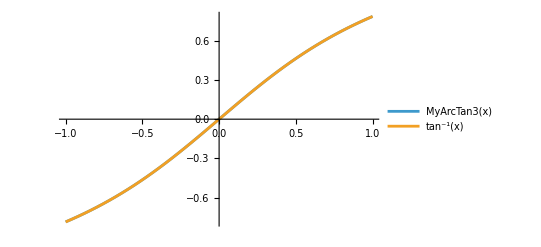

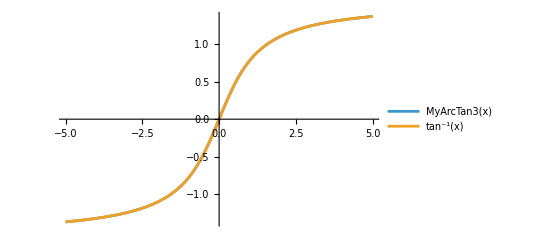

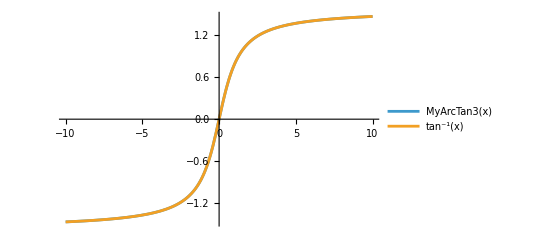

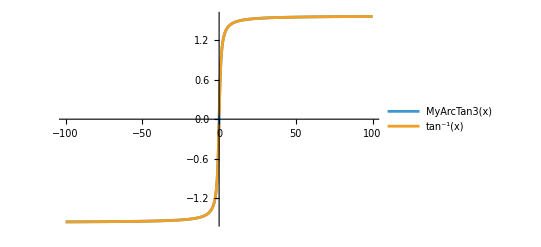

```mathematica
MyArcTan3[x_]:=Piecewise[{{p10[x],0<=x<=0.5},{Pi/4+p10[T[x]],0.5<x<=3},{Pi/2+p10[T[T[x]]],x>3},{-MyArcTan3[-x],x<0}}]
Plot[{MyArcTan3[x], ArcTan[x]},{x,-1,1},PlotLegends->"Expressions"]
Plot[{MyArcTan3[x], ArcTan[x]},{x,-5,5},PlotLegends->"Expressions"]
Plot[{MyArcTan3[x], ArcTan[x]},{x,-10,10},PlotLegends->"Expressions"]
Plot[{MyArcTan3[x], ArcTan[x]},{x,-100,100},PlotLegends->"Expressions"]
```

Podemos observar que la aproximación a Arctan resulta ser muy parecida/precisa.

### 5) Comparación de los errores. (terminada)

#### Solución

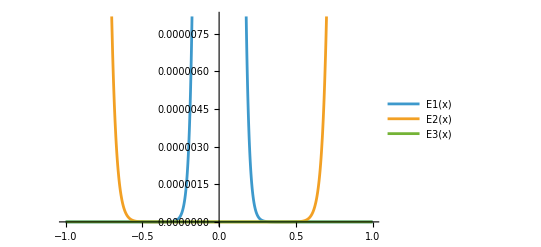

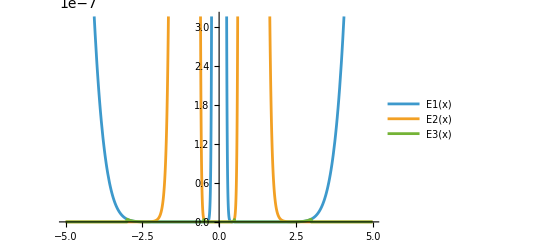

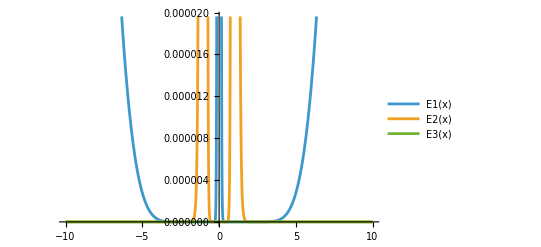

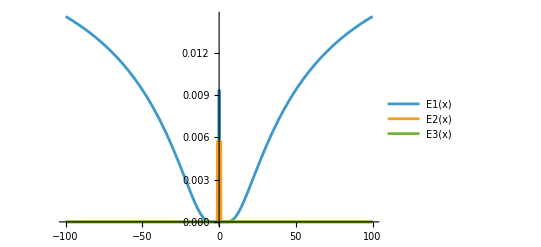

```mathematica
ClearAll["Global`*"]
(*MYARCTAN1*)
f[x_]:=ArcTan[x]
p[n_,x_]:=Sum[(-1)^k x^(2 k+1)/(2 k+1),{k,0,n}]
p10[x_] := p[10,x]
T[x_] := (x-1)/(x+1)
MyArcTan1[x_] := Piecewise[{{ (Pi/4) + p10[T[x]],x> 0},{-MyArcTan1[-x],x<0},{0, x==0}}]
(*MYARCTAN2*)
g[x_] := (Pi/2) -p10[1/x]
h[x_] := -(Pi/2) -p10[1/x]
MyArcTan2[x_] := Piecewise[{{ g[x],x> 1},{h[x],x<-1},{p10[x], -1<=x<=1}}]
(*MYARCTAN3*)
MyArcTan3[x_]:=Piecewise[{{p10[x],0<=x<=0.5},{Pi/4+p10[T[x]],0.5<x<=3},{Pi/2+p10[T[T[x]]],x>3},{-MyArcTan3[-x],x<0}}]
(*errores*)
E1[x_]:=Abs[ArcTan[x]-MyArcTan1[x]]
E2[x_]:=Abs[ArcTan[x]-MyArcTan2[x]]
E3[x_]:=Abs[ArcTan[x]-MyArcTan3[x]]
(*GRÁFICOS*)
Plot[{E1[x],E2[x],E3[x]},{x,-1,1},PlotLegends->"Expressions"]
Plot[{E1[x],E2[x],E3[x]},{x,-5,5},PlotLegends->"Expressions"]
Plot[{E1[x],E2[x],E3[x]},{x,-10,10},PlotLegends->"Expressions"]
Plot[{E1[x],E2[x],E3[x]},{x,-100,100},PlotLegends->"Expressions"]
```

1)determine cual de las tres implementaciones presenta, en general, un menor error;
R:  E3 presenta un menor error.

2) identifique en que zonas del dominio cada aproximación presenta sus mayores errores.
R:  E1 y E2 presentan picos  en la gráfica cuando se aproximan a -1 y 1.

3) analice que ocurre con los errores cuando se aumenta el tamaño del intervalo considerado.
R:  E3 se mantiene pegada al eje x (y=0), E2 hace lo mismo y E1 actúa de forma creciente a medida que el intervalo aumenta.

### 6) Comparación de las estrategias de reducción

#### Solución

Texto

```mathematica
ClearAll["Global`*"]
T[x_] = (x-1) / (x+1)


valores = {2,5,10,100}
tabla=Table[{x,MyArcTan1[x],MyArcTan2[x],MyArcTan3[x]},{x,valores}]
TableForm[tabla]
```

{2,5,10,100}

{{2,MyArcTan1[2],MyArcTan2[2],MyArcTan3[2]},{5,MyArcTan1[5],MyArcTan2[5],MyArcTan3[5]},{10,MyArcTan1[10],MyArcTan2[10],MyArcTan3[10]},{100,MyArcTan1[100],MyArcTan2[100],MyArcTan3[100]}}

2 | MyArcTan1[2] | MyArcTan2[2] | MyArcTan3[2]
5 | MyArcTan1[5] | MyArcTan2[5] | MyArcTan3[5]
10 | MyArcTan1[10] | MyArcTan2[10] | MyArcTan3[10]
100 | MyArcTan1[100] | MyArcTan2[100] | MyArcTan3[100]

### 7)

#### Solución

Texto

```mathematica
ClearAll["Global`*"]
```